# QCD calculation: Webber et al. Sec. 7

-Graphics-

We have learned how to sum/average helicities and polarizations.
Now it’s time to handle color; you will use ColourME[].

## Two-jet cross sections (Only QCD; mass ignored) : Ellis-Stirling-Webber Sec.7.5

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

### Create Topology (and also ignore helicities)

```mathematica
topologies=CreateTopologies[0,2->2];
_Hel=0;
```

### q q' -> q q'

loading generic model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

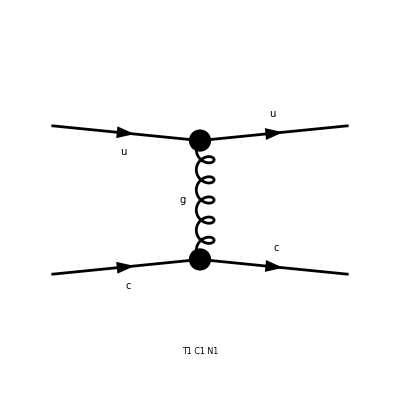

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
```

```mathematica
SquaredME[amp]//.HelicityME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

1/9 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2 (9 Mat[SUN1,SUN1]-3 (Mat[SUN1,SUN2]+Mat[SUN2,SUN1])+Mat[SUN2,SUN2])

```mathematica
%//.Abbr[]
```

1/9 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2 (9 Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col4] SUNT[Col2,Col3]]-3 (Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col3] SUNT[Col2,Col4]]+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col4] SUNT[Col2,Col3]])+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col3] SUNT[Col2,Col4]])

ColourME is called like HelicityME.

```mathematica
SquaredME[amp]//.HelicityME[amp]//.ColourME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

8 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2

```mathematica
%//.Subexpr[]//.{Alfas2->(gs^2/(4π))^2,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}
```

(gs^4 (T^2+(S-U)^2))/(2 T^2)

```mathematica
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

Now you notice that, while HelicityME takes AVARAGE, ColourME takes SUM!!!
This behavior can be summarized into two “lessons”:

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

```mathematica
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}//.U->-S-T]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### q q' -> q q' (Again)

Let’s do it again at a stretch.

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.Subexpr[]//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}//.U->-S-T]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### g q -> g q

Now you can calculate all the QCD tree-level diagrams.

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

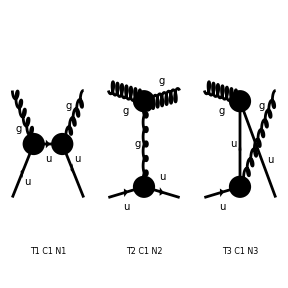

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

1/12 (128/3 Alfas2 (Abb9+2 MU2 Pair2 Pair9) π^2 Den[S,MU2]^2+32/3 Abb15 Alfas2 Pair2 π^2 Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])-32/3 Abb14 Alfas2 Pair1 Pair9 π^2 Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])-32/3 Abb1 Alfas2 Pair2 π^2 Pair1^* Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+32/3 Abb3 Alfas2 π^2 Pair2^* Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+8/3 Abb7 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0])^2-8/3 Alfas2 Pair1 π^2 (MU2-S) (MU2-U) Pair1^* (4 Den[S,MU2]+8 Den[T,0])^2+8/3 Abb8 Alfas2 Pair1 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0])^2+8/3 Alfas2 (-Abb10-2 MU2) Pair2 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0])^2-256/3 Abb21 Alfas2 π^2 Den[S,MU2] (Pair3 Den[S,MU2]+Pair5 Den[T,0])-64/3 Alfas2 (-Abb19+2 MU2 Pair2) π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (Pair3 Den[S,MU2]+Pair5 Den[T,0])+64/3 Alfas2 (Abb17+2 MU2 Pair8) π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (Pair3 Den[S,MU2]+Pair5 Den[T,0])+256/3 Abb5 Alfas2 π^2 Den[S,MU2] (Pair3^* Den[S,MU2]+Pair5^* Den[T,0])+64/3 Alfas2 (Abb12+2 MU2 Pair10) Pair2 π^2 (4 Den[S,MU2]+8 Den[T,0]) (Pair3^* Den[S,MU2]+Pair5^* Den[T,0])-64/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair9) π^2 (4 Den[S,MU2]+8 Den[T,0]) (Pair3^* Den[S,MU2]+Pair5^* Den[T,0])+512/3 Alfas2 (-Abb18-2 MU2) π^2 (Pair3 Den[S,MU2]+Pair5 Den[T,0]) (Pair3^* Den[S,MU2]+Pair5^* Den[T,0])-32/3 Alfas2 (Abb9+2 MU2 Pair2 Pair9) π^2 Den[S,MU2] Den[U,MU2]-4/3 Abb15 Alfas2 Pair2 π^2 (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]+4/3 Abb14 Alfas2 Pair1 Pair9 π^2 (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]+4/3 Abb1 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]-4/3 Abb3 Alfas2 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]+32/3 Abb21 Alfas2 π^2 (Pair3 Den[S,MU2]+Pair5 Den[T,0]) Den[U,MU2]-32/3 Abb5 Alfas2 π^2 (Pair3^* Den[S,MU2]+Pair5^* Den[T,0]) Den[U,MU2]+128/3 Alfas2 (Abb9+2 MU2 Pair2 Pair9) π^2 Den[U,MU2]^2+4/3 Abb15 Alfas2 Pair2 π^2 Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])-4/3 Abb14 Alfas2 Pair1 Pair9 π^2 Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])-4/3 Abb1 Alfas2 Pair2 π^2 Pair1^* Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+4/3 Abb3 Alfas2 π^2 Pair2^* Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+2/3 Abb7 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-2/3 Alfas2 Pair1 π^2 (MU2-S) (MU2-U) Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+2/3 Abb8 Alfas2 Pair1 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+2/3 Alfas2 (-Abb10-2 MU2) Pair2 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-8/3 Alfas2 (-Abb19+2 MU2 Pair2) π^2 Pair1^* (Pair3 Den[S,MU2]+Pair5 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+8/3 Alfas2 (Abb17+2 MU2 Pair8) π^2 Pair2^* (Pair3 Den[S,MU2]+Pair5 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+8/3 Alfas2 (Abb12+2 MU2 Pair10) Pair2 π^2 (Pair3^* Den[S,MU2]+Pair5^* Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-8/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair9) π^2 (Pair3^* Den[S,MU2]+Pair5^* Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb15 Alfas2 Pair2 π^2 Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])+32/3 Abb14 Alfas2 Pair1 Pair9 π^2 Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])+32/3 Abb1 Alfas2 Pair2 π^2 Pair1^* Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb3 Alfas2 π^2 Pair2^* Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])+8/3 Abb7 Alfas2 Pair2 π^2 Pair1^* (8 Den[T,0]+4 Den[U,MU2])^2-8/3 Alfas2 Pair1 π^2 (MU2-S) (MU2-U) Pair1^* (8 Den[T,0]+4 Den[U,MU2])^2+8/3 Abb8 Alfas2 Pair1 π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2])^2+8/3 Alfas2 (-Abb10-2 MU2) Pair2 π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2])^2-4/3 Abb21 Alfas2 π^2 Den[S,MU2] (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2])-1/3 Alfas2 (-Abb19+2 MU2 Pair2) π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2])+1/3 Alfas2 (Abb17+2 MU2 Pair8) π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2])+8/3 Alfas2 (-Abb18-2 MU2) π^2 (Pair3^* Den[S,MU2]+Pair5^* Den[T,0]) (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2])+32/3 Abb21 Alfas2 π^2 Den[U,MU2] (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2])-8/3 Alfas2 (-Abb19+2 MU2 Pair2) π^2 Pair1^* (8 Den[T,0]+4 Den[U,MU2]) (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2])+8/3 Alfas2 (Abb17+2 MU2 Pair8) π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2]) (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2])+4/3 Abb5 Alfas2 π^2 Den[S,MU2] (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2])+1/3 Alfas2 (Abb12+2 MU2 Pair10) Pair2 π^2 (4 Den[S,MU2]+8 Den[T,0]) (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2])-1/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair9) π^2 (4 Den[S,MU2]+8 Den[T,0]) (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2])+8/3 Alfas2 (-Abb18-2 MU2) π^2 (Pair3 Den[S,MU2]+Pair5 Den[T,0]) (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2])-32/3 Abb5 Alfas2 π^2 Den[U,MU2] (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2])+8/3 Alfas2 (Abb12+2 MU2 Pair10) Pair2 π^2 (8 Den[T,0]+4 Den[U,MU2]) (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2])-8/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair9) π^2 (8 Den[T,0]+4 Den[U,MU2]) (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2])+8/3 Alfas2 (-Abb18-2 MU2) π^2 (8 Pair5 Den[T,0]-8 Pair4 Den[U,MU2]) (8 Pair5^* Den[T,0]-8 Pair4^* Den[U,MU2]))

```mathematica
diag=InsertFields[topologies,{V[5],F[3,{1}]}->{V[5],F[3,{1}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
matrix=(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2/(3×8)
```

Now do PolarizationSum. As we want to take an average (the sum) over initial (final) photon, we divide the result by 2.

```mathematica
MyResult=1/2 PolarizationSum[matrix,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}//FullSimplify
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)//FullSimplify
```

preparing FORM code in /Users/misho/fc-pol-2.frm

running FORM...

ok

(gs^4 (-T (-36 S^3+21 S T^2+T^3)-19 T^2 (2 S+T) U+2 (-6 S+T) (6 S+T) U^2+36 T U^3))/(36 S T^2 U)

1/9 gs^4 (9/T^2-4/(S U)) (S^2+U^2)

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

We used GaugeTerms→False, because we know the diagram set is gauge-independent.
We can calculate with GaugeTerms and check that the result is independent of eta.
Let’s do it.

```mathematica
MyResultWithGaugeTerms=1/2 PolarizationSum[matrix,GaugeTerms->True]//.Subexpr[]//.Abbr[]//.Den[p2_,m2_]:>1/(p2-m2)
```

preparing FORM code in /Users/misho/fc-pol-2.frm

running FORM...

ok

-1/2 Alfas2 π^2 (-(16 (2 MU2^2 ((-T Pair[1]+1)/(Pair[1] 1)+1/1)+1-2 1))/T^2-(4 (1))/((-MU2+S) T)+(32 1)/(9 1)-(32 (1))/(9 ((11)^2)+(-(4 (1))/T-(4 1)/(9 1))/(-MU2+U))
 |  |  |  |

```mathematica
MyResultWithGaugeTerms//.MU2->(S+T+U)/2//Simplify
```

(8 Alfas2 π^2 (-9 S^6 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+36 S^5 T Pair[eta[1],k[3]] Pair[eta[3],k[1]]+8 S^4 T^2 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-89 S^3 T^3 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-58 S^2 T^4 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-11 S T^5 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-5 T^6 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+18 S^5 U Pair[eta[1],k[3]] Pair[eta[3],k[1]]-81 S^4 T U Pair[eta[1],k[3]] Pair[eta[3],k[1]]-32 S^3 T^2 U Pair[eta[1],k[3]] Pair[eta[3],k[1]]+31 S^2 T^3 U Pair[eta[1],k[3]] Pair[eta[3],k[1]]+88 S T^4 U Pair[eta[1],k[3]] Pair[eta[3],k[1]]+20 T^5 U Pair[eta[1],k[3]] Pair[eta[3],k[1]]+9 S^4 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+36 S^3 T U^2 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+12 S^2 T^2 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+133 S T^3 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-22 T^4 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-36 S^3 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+18 S^2 T U^3 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+40 S T^2 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-75 T^3 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+9 S^2 U^4 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-28 T^2 U^4 Pair[eta[1],k[3]] Pair[eta[3],k[1]]+18 S U^5 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-9 T U^5 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-9 U^6 Pair[eta[1],k[3]] Pair[eta[3],k[1]]-9 S^6 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+54 S^5 T Pair[eta[1],k[4]] Pair[eta[3],k[1]]+68 S^4 T^2 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-20 S^3 T^3 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-101 S^2 T^4 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-34 S T^5 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+42 T^6 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+18 S^5 U Pair[eta[1],k[4]] Pair[eta[3],k[1]]-144 S^4 T U Pair[eta[1],k[4]] Pair[eta[3],k[1]]-110 S^3 T^2 U Pair[eta[1],k[4]] Pair[eta[3],k[1]]-112 S^2 T^3 U Pair[eta[1],k[4]] Pair[eta[3],k[1]]+44 S T^4 U Pair[eta[1],k[4]] Pair[eta[3],k[1]]+112 T^5 U Pair[eta[1],k[4]] Pair[eta[3],k[1]]+9 S^4 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+126 S^3 T U^2 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-34 S^2 T^2 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+226 S T^3 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+17 T^4 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-36 S^3 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-54 S^2 T U^3 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+126 S T^2 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-94 T^3 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+9 S^2 U^4 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+36 S T U^4 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-50 T^2 U^4 Pair[eta[1],k[4]] Pair[eta[3],k[1]]+18 S U^5 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-18 T U^5 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-9 U^6 Pair[eta[1],k[4]] Pair[eta[3],k[1]]-18 S^5 T Pair[eta[1],k[3]] Pair[eta[3],k[2]]-52 S^4 T^2 Pair[eta[1],k[3]] Pair[eta[3],k[2]]-33 S^3 T^3 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+91 S^2 T^4 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+51 S T^5 Pair[eta[1],k[3]] Pair[eta[3],k[2]]-39 T^6 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+63 S^4 T U Pair[eta[1],k[3]] Pair[eta[3],k[2]]+66 S^3 T^2 U Pair[eta[1],k[3]] Pair[eta[3],k[2]]+123 S^2 T^3 U Pair[eta[1],k[3]] Pair[eta[3],k[2]]+120 S T^4 U Pair[eta[1],k[3]] Pair[eta[3],k[2]]-144 T^5 U Pair[eta[1],k[3]] Pair[eta[3],k[2]]-90 S^3 T U^2 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+42 S^2 T^2 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[2]]-33 S T^3 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[2]]-171 T^4 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+72 S^2 T U^3 Pair[eta[1],k[3]] Pair[eta[3],k[2]]-74 S T^2 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[2]]-57 T^3 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[2]]-36 S T U^4 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+18 T^2 U^4 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+9 T U^5 Pair[eta[1],k[3]] Pair[eta[3],k[2]]+8 S^4 T^2 Pair[eta[1],k[4]] Pair[eta[3],k[2]]+36 S^3 T^3 Pair[eta[1],k[4]] Pair[eta[3],k[2]]+48 S^2 T^4 Pair[eta[1],k[4]] Pair[eta[3],k[2]]+28 S T^5 Pair[eta[1],k[4]] Pair[eta[3],k[2]]+8 T^6 Pair[eta[1],k[4]] Pair[eta[3],k[2]]-12 S^3 T^2 U Pair[eta[1],k[4]] Pair[eta[3],k[2]]-20 S^2 T^3 U Pair[eta[1],k[4]] Pair[eta[3],k[2]]+76 S T^4 U Pair[eta[1],k[4]] Pair[eta[3],k[2]]-52 T^5 U Pair[eta[1],k[4]] Pair[eta[3],k[2]]-4 S^2 T^2 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[2]]+60 S T^3 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[2]]-132 T^4 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[2]]+12 S T^2 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[2]]-76 T^3 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[2]]-4 T^2 U^4 Pair[eta[1],k[4]] Pair[eta[3],k[2]]+63 S^5 T Pair[eta[1],k[3]] Pair[eta[3],k[3]]+74 S^4 T^2 Pair[eta[1],k[3]] Pair[eta[3],k[3]]-32 S^3 T^3 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+28 S^2 T^4 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+65 S T^5 Pair[eta[1],k[3]] Pair[eta[3],k[3]]-6 T^6 Pair[eta[1],k[3]] Pair[eta[3],k[3]]-171 S^4 T U Pair[eta[1],k[3]] Pair[eta[3],k[3]]-119 S^3 T^2 U Pair[eta[1],k[3]] Pair[eta[3],k[3]]-21 S^2 T^3 U Pair[eta[1],k[3]] Pair[eta[3],k[3]]-73 S T^4 U Pair[eta[1],k[3]] Pair[eta[3],k[3]]+68 T^5 U Pair[eta[1],k[3]] Pair[eta[3],k[3]]+144 S^3 T U^2 Pair[eta[1],k[3]] Pair[eta[3],k[3]]-19 S^2 T^2 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+16 S T^3 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+137 T^4 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[3]]-36 S^2 T U^3 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+99 S T^2 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+37 T^3 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+9 S T U^4 Pair[eta[1],k[3]] Pair[eta[3],k[3]]-35 T^2 U^4 Pair[eta[1],k[3]] Pair[eta[3],k[3]]-9 T U^5 Pair[eta[1],k[3]] Pair[eta[3],k[3]]+45 S^5 T Pair[eta[1],k[4]] Pair[eta[3],k[3]]+14 S^4 T^2 Pair[eta[1],k[4]] Pair[eta[3],k[3]]-101 S^3 T^3 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+71 S^2 T^4 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+88 S T^5 Pair[eta[1],k[4]] Pair[eta[3],k[3]]-53 T^6 Pair[eta[1],k[4]] Pair[eta[3],k[3]]-108 S^4 T U Pair[eta[1],k[4]] Pair[eta[3],k[3]]-41 S^3 T^2 U Pair[eta[1],k[4]] Pair[eta[3],k[3]]+122 S^2 T^3 U Pair[eta[1],k[4]] Pair[eta[3],k[3]]-29 S T^4 U Pair[eta[1],k[4]] Pair[eta[3],k[3]]-24 T^5 U Pair[eta[1],k[4]] Pair[eta[3],k[3]]+54 S^3 T U^2 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+27 S^2 T^2 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[3]]-77 S T^3 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+98 T^4 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+36 S^2 T U^3 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+13 S T^2 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+56 T^3 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[3]]-27 S T U^4 Pair[eta[1],k[4]] Pair[eta[3],k[3]]-13 T^2 U^4 Pair[eta[1],k[4]] Pair[eta[3],k[3]]+18 S^5 T Pair[eta[1],k[3]] Pair[eta[3],k[4]]+70 S^4 T^2 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+63 S^3 T^3 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+159 S^2 T^4 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+175 S T^5 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+27 T^6 Pair[eta[1],k[3]] Pair[eta[3],k[4]]-63 S^4 T U Pair[eta[1],k[3]] Pair[eta[3],k[4]]-96 S^3 T^2 U Pair[eta[1],k[3]] Pair[eta[3],k[4]]+S^2 T^3 U Pair[eta[1],k[3]] Pair[eta[3],k[4]]-150 S T^4 U Pair[eta[1],k[3]] Pair[eta[3],k[4]]-40 T^5 U Pair[eta[1],k[3]] Pair[eta[3],k[4]]+90 S^3 T U^2 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+8 S^2 T^2 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[4]]-177 S T^3 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+11 T^4 U^2 Pair[eta[1],k[3]] Pair[eta[3],k[4]]-72 S^2 T U^3 Pair[eta[1],k[3]] Pair[eta[3],k[4]]-8 S T^2 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+113 T^3 U^3 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+36 S T U^4 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+26 T^2 U^4 Pair[eta[1],k[3]] Pair[eta[3],k[4]]-9 T U^5 Pair[eta[1],k[3]] Pair[eta[3],k[4]]+10 S^4 T^2 Pair[eta[1],k[4]] Pair[eta[3],k[4]]-6 S^3 T^3 Pair[eta[1],k[4]] Pair[eta[3],k[4]]+202 S^2 T^4 Pair[eta[1],k[4]] Pair[eta[3],k[4]]+198 S T^5 Pair[eta[1],k[4]] Pair[eta[3],k[4]]-20 T^6 Pair[eta[1],k[4]] Pair[eta[3],k[4]]-18 S^3 T^2 U Pair[eta[1],k[4]] Pair[eta[3],k[4]]+144 S^2 T^3 U Pair[eta[1],k[4]] Pair[eta[3],k[4]]-106 S T^4 U Pair[eta[1],k[4]] Pair[eta[3],k[4]]-132 T^5 U Pair[eta[1],k[4]] Pair[eta[3],k[4]]+54 S^2 T^2 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[4]]-270 S T^3 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[4]]-28 T^4 U^2 Pair[eta[1],k[4]] Pair[eta[3],k[4]]-94 S T^2 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[4]]+132 T^3 U^3 Pair[eta[1],k[4]] Pair[eta[3],k[4]]+48 T^2 U^4 Pair[eta[1],k[4]] Pair[eta[3],k[4]]+Pair[eta[1],k[1]] ((9 S^6-63 T^6-102 T^5 U+35 T^4 U^2+84 T^3 U^3+19 T^2 U^4+18 T U^5+9 U^6-18 S^5 (2 T+U)+S^4 (-7 T^2+90 T U-9 U^2)+2 S^3 (91 T^3-12 T^2 U-36 T U^2+18 U^3)+S^2 (157 T^4-240 T^3 U+88 T^2 U^2+36 T U^3-9 U^4)-2 S (25 T^5+53 T^4 U+13 T^3 U^2+38 T^2 U^3+18 T U^4+9 U^5)) Pair[eta[3],k[1]]+T (18 S^5+S^4 (53 T-54 U)-T (T+U)^2 (29 T^2-120 T U+27 U^2)+2 S^3 (63 T^2-61 T U+27 U^2)-2 S T (56 T^3+69 T^2 U-70 T U^2-19 U^3)+2 S^2 (4 T^3-166 T^2 U+29 T U^2-9 U^3)) Pair[eta[3],k[2]]+9 S^6 Pair[eta[3],k[3]]-27 S^5 T Pair[eta[3],k[3]]+40 S^4 T^2 Pair[eta[3],k[3]]+75 S^3 T^3 Pair[eta[3],k[3]]-16 S^2 T^4 Pair[eta[3],k[3]]+80 S T^5 Pair[eta[3],k[3]]+95 T^6 Pair[eta[3],k[3]]-54 S^5 U Pair[eta[3],k[3]]+54 S^4 T U Pair[eta[3],k[3]]+3 S^3 T^2 U Pair[eta[3],k[3]]+94 S^2 T^3 U Pair[eta[3],k[3]]+93 S T^4 U Pair[eta[3],k[3]]+98 T^5 U Pair[eta[3],k[3]]+135 S^4 U^2 Pair[eta[3],k[3]]-36 S^3 T U^2 Pair[eta[3],k[3]]+33 S^2 T^2 U^2 Pair[eta[3],k[3]]-259 S T^3 U^2 Pair[eta[3],k[3]]-39 T^4 U^2 Pair[eta[3],k[3]]-180 S^3 U^3 Pair[eta[3],k[3]]+54 S^2 T U^3 Pair[eta[3],k[3]]-235 S T^2 U^3 Pair[eta[3],k[3]]+90 T^3 U^3 Pair[eta[3],k[3]]+135 S^2 U^4 Pair[eta[3],k[3]]-81 S T U^4 Pair[eta[3],k[3]]+159 T^2 U^4 Pair[eta[3],k[3]]-54 S U^5 Pair[eta[3],k[3]]+36 T U^5 Pair[eta[3],k[3]]+9 U^6 Pair[eta[3],k[3]]-18 S^5 T Pair[eta[3],k[4]]-71 S^4 T^2 Pair[eta[3],k[4]]-156 S^3 T^3 Pair[eta[3],k[4]]-258 S^2 T^4 Pair[eta[3],k[4]]-114 S T^5 Pair[eta[3],k[4]]+41 T^6 Pair[eta[3],k[4]]+54 S^4 T U Pair[eta[3],k[4]]+152 S^3 T^2 U Pair[eta[3],k[4]]+208 S^2 T^3 U Pair[eta[3],k[4]]+168 S T^4 U Pair[eta[3],k[4]]+122 T^5 U Pair[eta[3],k[4]]-54 S^3 T U^2 Pair[eta[3],k[4]]-108 S^2 T^2 U^2 Pair[eta[3],k[4]]+70 S T^3 U^2 Pair[eta[3],k[4]]-24 T^4 U^2 Pair[eta[3],k[4]]+18 S^2 T U^3 Pair[eta[3],k[4]]+44 S T^2 U^3 Pair[eta[3],k[4]]-122 T^3 U^3 Pair[eta[3],k[4]]-17 T^2 U^4 Pair[eta[3],k[4]])+Pair[eta[1],k[2]] ((9 S^6-24 T^6-10 T^5 U+21 T^4 U^2-72 T^3 U^3-70 T^2 U^4+18 T U^5+9 U^6-18 S^5 (3 T+U)-3 S^4 (8 T^2-48 T U+3 U^2)+2 S^3 (63 T^3-13 T^2 U-63 T U^2+18 U^3)+S^2 (7 T^4-266 T^3 U+54 T^2 U^2+54 T U^3-9 U^4)-2 S (52 T^5+60 T^4 U-106 T^3 U^2-33 T^2 U^3+18 T U^4+9 U^5)) Pair[eta[3],k[1]]+T (2 T (18 S^4+5 T^4+S^3 (35 T-62 U)+77 T^3 U+85 T^2 U^2-45 T U^3-58 U^4+S^2 (-71 T^2-179 T U+12 U^2)+S (-83 T^3-76 T^2 U+189 T U^2+90 U^3)) Pair[eta[3],k[2]]+(-45 S^5+S^4 (-58 T+108 U)+S^3 (-5 T^2+177 T U-54 U^2)+S^2 (23 T^3+256 T^2 U-47 T U^2-36 U^3)+S (50 T^4+105 T^3 U-361 T^2 U^2-205 T U^3+27 U^4)+T (35 T^4-78 T^3 U-136 T^2 U^2+110 T U^3+133 U^4)) Pair[eta[3],k[3]]+2 T (-27 S^4+T^4+15 T^3 U-5 T^2 U^2+17 T U^3+36 U^4+S^3 (-50 T+77 U)+S^2 (-54 T^2+117 T U-37 U^2)-S (30 T^3-91 T^2 U+84 T U^2+49 U^3)) Pair[eta[3],k[4]]))))/(9 T^2 (S+T-U)^2 (-S+T+U)^2 Pair[eta[1],k[1]] Pair[eta[3],k[3]])

It seems that this amplitude depends on “eta”, and thus gauge-dependent. However, note that, in this 2→2 process, k[1]+k[2]==k[3]+k[4]. Therefore...

```mathematica
%//.{Pair[eta_,k[2]]:>Pair[eta,k[3]]+Pair[eta,k[4]]-Pair[eta,k[1]]}//Simplify
```

1/(9 T^2 (S+T-U)^2 (-S+T+U)^2)8 Alfas2 π^2 (9 S^6+21 T^6+18 S^5 (2 T-3 U)+84 T^5 U+111 T^4 U^2+136 T^3 U^3+115 T^2 U^4+36 T U^5+9 U^6+S^4 (115 T^2-108 T U+135 U^2)+4 S^3 (34 T^3-43 T^2 U+18 T U^2-45 U^3)+S^2 (111 T^4-136 T^3 U+114 T^2 U^2+72 T U^3+135 U^4)+2 S (42 T^5+T^4 U-68 T^3 U^2-86 T^2 U^3-54 T U^4-27 U^5))

And we just have confirmed that this amplitude is gauge independent.
Needless to say, this agrees with the result in the canon.

```mathematica
FullSimplify[%==WebberResult,Assumptions->{S+T+U==2MU2,MU2==0,Alfas2==(gs^2/(4π))^2}]
```

True

## Summary of Calculation

```mathematica
Exit[];
```

```mathematica
(* SET UP *)
$Language="English";
<<FeynArts`
<<FormCalc`

(* Topology *)
topologies=CreateTopologies[0,2->2];

(* Diagram *)
diag=InsertFields[topologies,
{V[5],F[3,{1}]}->{V[5],F[3,{1}]},
InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];

Paint[diag];
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

loading generic model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

-Graphics-

```mathematica
(* Amplitude *)
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
squ=SquaredME[amp];

(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(2×squ)//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)

(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/(3×8);

(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

matrix = PolarizationSum[squ,GaugeTerms->False]/2; (* Asserting gauge invariance! *)

FullSimplify[matrix]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/misho/fc-pol-2.frm

running FORM...

ok

4/9 Alfas2 π^2 (16 Sub9 Den[S,MU2]^2+Den[S,MU2] (18 Sub7 Den[T,0]-Sub4 Den[U,MU2])+2 (36 Sub10 Den[T,0]^2+9 Sub13 Den[T,0] Den[U,MU2]-8 Sub2 Den[U,MU2]^2))

```mathematica
MyResult=FullSimplify[%//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}]
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)
```

(gs^4 (-T (-36 S^3+21 S T^2+T^3)-19 T^2 (2 S+T) U+2 (-6 S+T) (6 S+T) U^2+36 T U^3))/(36 S T^2 U)

gs^4 ((S^2+U^2)/T^2-(4 (S^2+U^2))/(9 S U))

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

DIVIDE by INITIAL vector particles.